### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

```mathematica
Half[list_]:= Take[list, Floor[Length[list]/2]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;srcblocks=4;
(*------------------------*)
SeedRandom[15]
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*srcblocks];
dwKer = RandomInteger[{-16,16},td*srcblocks];
```

```mathematica
data
```

{7,3,13,14,-10,-12,9,15,-14,-3,11,-10,13,11,6,-8,2,-4,14,-1,-8,2,12,9,6,-9,2,-4,-8,-1,-11,-9,13,7,14,2,3,-16,-7,0,1,-4,-1,-15,-5,1,-1,-16,2,-4,-12,6,4,6,-8,-5,12,14,8,-6,7,-10,-13,2,-4,-13,11,5,-13,7,6,2,-15,11,6,-16,6,12,8,16,14,10,14,15,13,4,-16,7,15,-14,-13,-4,-7,5,-15,4,-15,6,-2,5}

```mathematica
expected=Downsample[ListConvolve[dwKer,data,1,0],3,3]
```

{-153,150,39,164,-490,339,-409,207,-205,-125,-163,212,370,-461,27,-168,-3,-414,-39,-47,369,-495,-89,-148,-15,10,250,556,273,91,-70,-794,420}

```mathematica
Max[Abs[expected]]
```

794

```mathematica
Export[RelativeDir["data.dat"],ToText[data]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];
Export[RelativeDir["dwsamp_coefs.dat"],ToText[dwKer]];
```

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

Operations:

```mathematica
Downsample[result,3]
```

{0,0,0,0,0,-23,-269,266,354,-320,11,-423,457,-452,-158,24,-48,345,-276,54,-265,180,-218,-215,-421,461,-308,-11,16,-170,-72,138,496,-74,504,158,-725,171,-82,143,-115,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### After simulation:

```mathematica
ker
```

{9,3,-4,-15,-10,-4,-10,-15,12,9,0,3}

```mathematica
expected
```

{21,9,102,153,18,131,-148,-605,-282,255,-214,-582,406,489,-205,36,152,-150,-248,-158,-179,29,-331,66,383,194,-250,-239,-232,29,-428,-365,98,145,403,633,229,102,-103,-332,-644,-317,-41,87,153,336,19,149,98,-70,-1,528,76,-7,317,315,44,-138,114,307,-53,-414,-144,-5,-596,-498,163,128,165,731,124,-125,247,118,-358,-311,406,-58,-386,364,492,-11,95,-11,-146,-317,-571,-514,-694,-647,114,-174,-700,74,447,157,-48,42,509,234}

```mathematica
upKer
```

{2,-4,12,2,0,-1,0,7,2,16,-3,-5,-10,11,-8,13,9,8}

```mathematica
Max[lol]
```

18964

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{21,0,0,9,0,0,102,0,0,153,0,0,18,0,0,131,0,0,-148,0,0,-605,0,0,-282,0,0,255,0,0,-214,0,0,-582,0,0,406,0,0,489,0,0,-205,0,0,36,0,0,152,0,0,-150,0,0,-248,0,0,-158,0,0,-179,0,0,29,0,0,-331,0,0,66,0,0,383,0,0,194,0,0,-250,0,0,-239,0,0,-232,0,0,29,0,0,-428,0,0,-365,0,0,98,0,0,145,0,0,403,0,0,633,0,0,229,0,0,102,0,0,-103,0,0,-332,0,0,-644,0,0,-317,0,0,-41,0,0,87,0,0,153,0,0,336,0,0,19,0,0,149,0,0,98,0,0,-70,0,0,-1,0,0,528,0,0,76,0,0,-7,0,0,317,0,0,315,0,0,44,0,0,-138,0,0,114,0,0,307,0,0,-53,0,0,-414,0,0,-144,0,0,-5,0,0,-596,0,0,-498,0,0,163,0,0,128,0,0,165,0,0,731,0,0,124,0,0,-125,0,0,247,0,0,118,0,0,-358,0,0,-311,0,0,406,0,0,-58,0,0,-386,0,0,364,0,0,492,0,0,-11,0,0,95,0,0,-11,0,0,-146,0,0,-317,0,0,-571,0,0,-514,0,0,-694,0,0,-647,0,0,114,0,0,-174,0,0,-700,0,0,74,0,0,447,0,0,157,0,0,-48,0,0,42,0,0,509,0,0,234}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{168,189,273,-96,312,-93,639,954,1572,405,2619,1113,-1593,1602,378,586,1548,4031,-2010,1090,-2724,-3204,-7748,-3779,5404,-8444,358,7110,-100,-3247,-1832,-3034,-9878,-5954,-9739,-2852,2506,2099,5900,-493,10243,-7069,-5472,-2778,-977,-1691,300,8750,-4459,8130,-2016,1377,-2845,-1104,4601,-6042,1276,-722,-1816,-2312,1052,-3799,-4339,3932,-3578,-357,-3853,-2629,-8253,-145,-3395,3820,2532,6001,-1651,-4681,4160,-552,-4656,-919,334,-4154,-1478,1967,2103,-2873,-3728,7185,-4856,27,-396,-5286,-9678,-2866,-8704,-979,3266,-690,-2866,-1468,1410,-5341,1620,2257,4559,-3460,12093,4933,-9435,10290,2561,-2344,3967,9650,-182,3359,2401,2319,-4436,418,5590,-10957,-4976,6716,-10578,-2331,6091,-4656,-7669,417,-2813,-4401,-3241,1566,-1489,-6464,6735,2308,-6890,5285,-1381,-913,1777,7215,1060,4468,568,-551,-478,1472,4373,-1374,2965,4857,5561,6090,-2061,5409,-3814,-2060,-1210,7653,2429,6524,5265,-369,6879,1867,2493,749,3702,-1478,212,2944,2025,1609,4186,5811,3471,1907,10,332,-1217,-3529,-4608,-128,1269,-2990,1372,4137,-1214,-4407,-1099,-9113,-9494,299,-11819,-1528,3434,-602,-3553,-705,843,-8232,-979,-1062,2271,-2440,11535,7713,-11564,11550,-3728,-3489,-1451,9413,5189,5081,7031,1090,4362,-1144,3355,-6464,-172,1893,-5858,1423,6015,2633,2904,-27,1383,-9060,-3502,-7979,1578,3117,3478,6326,-1300,10428,-3230,-1686,-105,1457,-1194,2038,8329,-4805,5967,-1313,2299,-3253,1444,4792,-5729,-1875,-1551,-8221,-6421,2900,-11358,-5876,795,-12362,-13332,369,-15328,-10621,5297,-6339,-4928,-6795,-945,-15924,-11546,-11029,-7952,-391,-2938,2496,-1742,8307,-7195,-2548,752,-1365,-5115,1168,3210,-7645,5308,2286,4731,5990,6471,2701}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{0,0,1,-1,1,-1,2,3,6,1,10,4,-7,6,1,2,6,15,-8,4,-11,-13,-31,-15,21,-33,1,27,-1,-13,-8,-12,-39,-24,-39,-12,9,8,23,-2,40,-28,-22,-11,-4,-7,1,34,-18,31,-8,5,-12,-5,17,-24,4,-3,-8,-10,4,-15,-17,15,-14,-2,-16,-11,-33,-1,-14,14,9,23,-7,-19,16,-3,-19,-4,1,-17,-6,7,8,-12,-15,28,-19,0,-2,-21,-38,-12,-34,-4,12,-3,-12,-6,5,-21,6,8,17,-14,47,19,-37,40,10,-10,15,37,-1,13,9,9,-18,1,21,-43,-20,26,-42,-10,23,-19,-30,1,-11,-18,-13,6,-6,-26,26,9,-27,20,-6,-4,6,28,4,17,2,-3,-2,5,17,-6,11,18,21,23,-9,21,-15,-9,-5,29,9,25,20,-2,26,7,9,2,14,-6,0,11,7,6,16,22,13,7,0,1,-5,-14,-18,-1,4,-12,5,16,-5,-18,-5,-36,-38,1,-47,-6,13,-3,-14,-3,3,-33,-4,-5,8,-10,45,30,-46,45,-15,-14,-6,36,20,19,27,4,17,-5,13,-26,-1,7,-23,5,23,10,11,-1,5,-36,-14,-32,6,12,13,24,-6,40,-13,-7,-1,5,-5,7,32,-19,23,-6,8,-13,5,18,-23,-8,-7,-33,-26,11,-45,-23,3,-49,-53,1,-60,-42,20,-25,-20,-27,-4,-63,-46,-44,-32,-2,-12,9,-7,32,-29,-10,2,-6,-20,4,12,-30,20,8,18,23,25,10}

```mathematica
result
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,3,3,4,6,6,11,12,13,14,15,13,12,11,6,6,-3,-6,-10,-17,-18,-21,-21,-21,-19,-19,-10,-6,-2,9,9,18,21,23,26,27,22,20,17,7,8,-10,-15,-22,-34,-35,-44,-45,-46,-42,-46,-15,-5,9,36,31,102,118,141,166,162,236,244,261,247,245,285,276,277,217,220,213,192,178,100,105,74,54,39,-16,-12,-29,-35,-40,-50,-47,-41,-36,-31,-14,-14,-1,4,9,21,20,24,24,24,20,20,12,8,4,-7,-7,-15,-18,-20,-24,-24,-20,-18,-16,-7,-7,1,4,7,14,13,14,14,14,11,10,9,7,6,1,2,1,1,1,-1,0,-1,-1,-1,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-3,-3,-3,-2,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-3,-3,-2,-2,-3,-3,-3,-3,-3,-3,-3,-3,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-3,-3,-3,-2,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-3,-3,-2,-2,-3,-3,-3,-3,-3,-3,-3,-3,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-3,-3,-3,-2,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-3,-3,-2,-2,-3,-3,-3,-3,-3,-3,-3,-3,-2,-2,-2,-1,-2,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-2,-2,-2,-1,-1,-2,-1,-2,-2,-2,-2,-3,-3,-3,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-3,-2,-2,-3,-2,-2,-2,-2,-2,-2,-3,-2,-2,-3,-3,-4,-4,-3,-7,-7,-9,-9,-9,-15,-16,-17,-17,-18,-17,-16,-14,-9,-9,0,4,7,15,15,18,19,18,16,16,6,3,-2,-12,-12,-22,-24,-27,-29,-30,-26,-24,-21,-11,-12,6,12,19,31,33,41,43,44,40,44,12,2,-12,-39,-35,-106,-122,-145,-169,-164,-240,-247,-264,-250,-248,-289,-280,-281,-221,-224,-217,-195,-182,-103,-108,-77,-57,-43,13,9,26,32,36,47,44,38,33,28,11,12,-2,-7,-12,-24,-23,-28,-28,-28,-24,-24,-16,-12,-8,4,4,12,15,17,21,21,17,15,12,4,4,-4,-7,-9,-16,-15,-17,-16,-16,-13,-12,-11,-10,-9,-4,-4,-4,-3,-3,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{27}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["coefs.dat"]]
```

{1022,1804,0,-2204,-1533,1752,3307,0,-4960,-4087,6131,19840,26214,19840,6131,-4087,-4960,0,3307,1752,-1533,-2204,0,1804,1022}

```mathematica
fupker =  Flatten@Import[RelativeDir["upsamp_coefs.dat"]]
```

{-4901,17651,21709,30304,39407,47324,52851,54718,52851,47324,39407,30304,21709,17651,-4901}

```mathematica
datain=Downsample[Flatten@Import[RelativeDir["data.dat"]],3]
```

{339,811,123,-741,-546,430,791,21,-779,-465,514,758,-82,-805,-376,590,713,-184,-818,-282,657,657,-282,-818,-184,713,590,-376,-805,-82,758,514,-465,-779,21,791,430,-546,-741,123,811,339,-618,-692,224,819,243,-680,-631,321,814,143,-732,-561,413,796,41,-772,-482,498,765,-62,-801,-395,576,723,-164,-816,-302,644,669,-263,-819,-204,702,604,-358,-808,-103,750,530,-448,-785,0,785,448,-530,-750,103,808,358,-604,-702,204,819,263,-669,-644,302,816,164,-723,-576,395,801,62,-765,-498,482,772,-41,-796,-413,561,732,-143,-814,-321,631,680,-243,-819,-224,692,618,-339,-811,-123,741,546,-430,-791,-21,779,465,-514,-758,82,805,376,-590,-713,184,818,282,-657,-657,282,818,184,-713,-590,376,805,82,-758,-514,465,779,-21,-791,-430,546,741,-123,-811,-339,618,692,-224,-819,-243,680,631,-321,-814,-143,732,561,-413,-796,-41,772,482,-498,-765,62,801,395,-576,-723,164,816,302,-644,-669,263,819,204,-702,-604,358,808,103,-750,-530,448,785,0,-785,-448,530,750,-103,-808,-358,604,702,-204,-819,-263,669,644,-302,-816,-164,723,576,-395,-801,-62,765,498,-482,-772,41,796,413,-561,-732,143,814,321,-631,-680,243,819,224,-692,-618,339,811,123,-741,-546,430,791,21,-779,-465,514,758,-82,-805,-376,590,713,-184,-818,-282,657,657,-282,-818,-184,713,590,-376,-805,-82,758,514,-465,-779,21,791,430,-546,-741,123,811,339,-618,-692,224,819,243,-680,-631,321,814,143,-732,-561,413,796,41,-772,-482,498,765,-62,-801,-395,576,723,-164,-816,-302,644,669,-263,-819,-204,702,604,-358,-808,-103,750,530,-448,-785}

```mathematica
Floor[ListConvolve[Reverse[fker],datain,1,0]/2^12]
```

{84,351,387,-314,-1026,-358,1360,1632,-841,-3198,-1092,5142,9185,5687,-2447,-6501,-2290,4445,5096,-895,-5468,-2635,3633,4854,-510,-4991,-2333,3663,4421,-1145,-5076,-1750,4080,4080,-1750,-5076,-1145,4421,3663,-2333,-4991,-510,4700,3188,-2884,-4833,130,4908,2668,-3388,-4602,761,5030,2101,-3839,-4294,1387,5082,1510,-4221,-3913,1993,5051,887,-4546,-3480,2562,4941,256,-4794,-2989,3087,4743,-391,-4974,-2451,3573,4487,-1017,-5069,-1876,3995,4150,-1632,-5084,-1272,4352,3746,-2221,-5014,-637,4651,3287,-2779,-4874,0,4873,2778,-3288,-4652,636,5013,2220,-3747,-4353,1271,5083,1631,-4151,-3996,1875,5068,1016,-4488,-3574,2450,4973,390,-4744,-3088,2988,4793,-257,-4942,-2563,3479,4545,-888,-5052,-1994,3912,4220,-1511,-5083,-1388,4293,3838,-2102,-5031,-762,4601,3387,-2669,-4909,-131,4832,2883,-3189,-4701,509,4990,2332,-3664,-4422,1144,5075,1749,-4081,-4081,1749,5075,1144,-4422,-3664,2332,4990,509,-4701,-3189,2883,4832,-131,-4909,-2669,3387,4601,-762,-5031,-2102,3838,4293,-1388,-5083,-1511,4220,3912,-1994,-5052,-888,4545,3479,-2563,-4942,-257,4793,2988,-3088,-4744,390,4973,2450,-3574,-4488,1016,5068,1875,-3996,-4151,1631,5083,1271,-4353,-3747,2220,5013,636,-4652,-3288,2778,4873,0,-4874,-2779,3287,4651,-637,-5014,-2221,3746,4352,-1272,-5084,-1632,4150,3995,-1876,-5069,-1017,4487,3573,-2451,-4974,-391,4743,3087,-2989,-4794,256,4941,2562,-3480,-4546,887,5051,1993,-3913,-4221,1510,5082,1387,-4294,-3839,2101,5030,761,-4602,-3388,2668,4908,130,-4833,-2884,3188,4700,-510,-4991,-2333,3663,4421,-1145,-5076,-1750,4080,4080,-1750,-5076,-1145,4421,3663,-2333,-4991,-510,4700,3188,-2884,-4833,130,4908,2668,-3388,-4602,761,5030,2101,-3839,-4294,1387,5082,1510,-4221,-3913,1993,5051,887,-4546,-3480,2562,4941,256,-4794,-2989,3087,4743,-391,-4974,-2451,3573,4487,-1017,-5069,-1876,3995,4150}

```mathematica
Floor[764980/2^12]
```

186

```mathematica
Floor[ListConvolve[Reverse[fupker], Flatten[Riffle[Floor[ListConvolve[Reverse[fker],datain]/2^12],{{0,0}}]]]/2^20]
```

{-3,109,166,316,330,200,182,79,-53,-213,-286,-231,-305,-243,-80,39,147,185,326,326,185,147,39,-80,-243,-305,-231,-286,-213,-53,79,182,200,330,316,166,109,-3,-106,-269,-318,-227,-262,-179,-24,119,216,213,329,301,144,68,-45,-132,-291,-327,-220,-235,-142,5,157,246,222,323,282,121,27,-86,-155,-309,-332,-210,-204,-104,34,191,271,227,312,257,94,-15,-126,-175,-322,-330,-196,-170,-64,62,224,293,230,297,230,68,-56,-162,-192,-329,-323,-178,-132,-22,90,253,310,229,276,198,40,-96,-198,-207,-332,-312,-159,-94,19,116,278,322,224,251,164,11,-135,-229,-218,-329,-295,-136,-53,60,139,297,328,214,221,125,-19,-173,-258,-227,-321,-274,-112,-12,100,162,313,330,203,190,87,-47,-206,-282,-231,-308,-249,-86,29,139,181,324,327,188,154,46,-75,-237,-302,-232,-291,-220,-59,70,175,197,329,318,169,116,5,-102,-264,-316,-228,-267,-186,-29,111,209,211,330,304,149,76,-37,-127,-287,-326,-222,-241,-150,-1,149,240,221,325,286,126,36,-77,-150,-306,-331,-212,-210,-112,28,185,266,227,315,263,100,-6,-117,-170,-319,-330,-198,-176,-71,58,218,289,231,300,236,74,-47,-155,-189,-328,-325,-182,-140,-31,85,248,307,230,281,205,46,-88,-191,-204,-332,-315,-163,-102,11,111,273,320,226,257,172,18,-127,-222,-215,-329,-298,-140,-61,52,135,294,328,217,228,134,-12,-165,-252,-225,-323,-279,-117,-20,92,157,311,330,206,196,95,-41,-199,-277,-230,-311,-254,-91,21,131,177,322,328,191,161,54,-69,-231,-298,-231,-294,-225,-63,63,169,195,329,321,174,124,14,-96,-258,-313,-229,-272,-192,-35,103,203,209,330,308,153,85,-28,-122,-283,-325,-224,-247,-158,-7,141,234,219,326,290,130,44,-69,-145,-302,-330,-214,-217,-120,22,178,261,226,317,268,105,2,-110,-167,-317,-331,-201,-183,-80,52,212,285,230,303,242,79,-40,-148,-186,-327,-327,-186,-148,-40,79,242,303,230,285,212,52,-80,-183,-201,-331,-317,-167,-110,2,105,268,317,226,261,178,22,-120,-217,-214,-330,-302,-145,-69,44,130,290,326,219,234,141,-7,-158,-247,-224,-325,-283,-122,-28,85,153,308,330,209,203,103,-35,-192,-272,-229,-313,-258,-96,14,124,174,321,329,195,169,63,-63,-225,-294,-231,-298,-231,-69,54,161,191,328,322,177,131,21,-91,-254,-311,-230,-277,-199,-41,95,196,206,330,311,157,92,-20,-117,-279,-323,-225,-252,-165,-12,134,228,217,328,294,135,52,-61,-140,-298,-329,-215,-222,-127,18,172,257,226,320,273,111,11,-102,-163,-315,-332,-204,-191,-88,46,205,281,230,307,248,85,-31,-140,-182,-325,-328,-189,-155,-47,74,236,300,231,289,218,58,-71,-176,-198,-330,-319,-170,-117,-6,100,263,315,227,266,185,28,-112,-210,-212,-331,-306,-150,-77,36,126,286,325,221,240,149,-1,-150,-241,-222,-326,-287,-127,-37,76,149,304,330,211,209,111,-29,-186,-267,-228,-316,-264,-102,5,116,169,318,329,197,175,70,-59,-220,-291,-232,-302,-237,-75,46,154,188,327,324,181,139,29,-86,-249,-308,-231,-282,-206,-47,87,190,203,330,313,162,100,-12,-112,-274,-321,-227,-258,-173,-19,125,221,214,328,297,139,60,-53,-136,-295,-329,-218,-229,-135,11,164,251,224,322,278,116,19,-94,-159,-312,-332,-207,-198,-96,40,198,276,229,310,253,90,-22,-132,-178,-323,-329,-192,-162,-56,68,230,297,230,293,224,62,-64,-170,-196,-330,-322,-175,-126,-15,94,257,312,227,271,191,34,-104,-204,-210,-332,-309,-155,-86,27,121,282,323,222,246,157,5,-142,-235,-220,-327,-291,-132,-45,68,144,301,329,213,216,119,-24,-179,-262,-227,-318,-269,-106,-3,109,166,316,330,200,182,79,-53,-213,-286,-231,-305,-243,-80,39,147,185,326,326,185,147,39,-80,-243,-305,-231,-286,-213,-53,79,182,200,330,316,166,109,-3,-106,-269,-318,-227,-262,-179,-24,119,216,213,329,301,144,68,-45,-132,-291,-327,-220,-235,-142,5,157,246,222,323,282,121,27,-86,-155,-309,-332,-210,-204,-104,34,191,271,227,312,257,94,-15,-126,-175,-322,-330,-196,-170,-64,62,224,293,230,297,230,68,-56,-162,-192,-329,-323,-178,-132,-22,90,253,310,229,276,198,40,-96,-198,-207,-332,-312,-159,-94,19,116,278,322,224,251,164,11,-135,-229,-218,-329,-295,-136,-53,60,139,297,328,214,221,125,-19,-173,-258,-227,-321,-274,-112,-12,100,162,313,330,203,190,87,-47,-206,-282,-231,-308,-249}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap20.dat"]];
```

```mathematica
(*afirIn = snaps[[2]]*)
```

```mathematica
(*afirOut = snaps[[10]]*)
```

```mathematica
(*expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]*)
```

```mathematica
(*LongestCommonSubsequence[afirOut,expafirOut]*)
```

```mathematica
snaps[[2]]
```

{-4350,-4118,-4022,-4308,-4300,-3796,-4202,-4350,-3486,-4022,-4308,-3121,-3796,-4202,-2666,-3486,-4022,-2165,-3121,-3796,-1690,-2666,-3486,-1190,-2165,-3121,-649,-1690,-2666,-124,-1190,-2165,417,-649,-1690,940,-124,-1190,1410,417,-649,1895,940,-124,2395,1410,417,2863,1895,940,3245,2395,1410,3559,2863,1895,3816,3245,2395,4021,3559,2863,4141,3816,3245,4177,4021,3559,4204,4141,3816,4100,4177,4021,3865,4204,4141,3490,4100,4177,2976,3865,4204,2295,3490,4100,1562,2976,3865,832,2295,3490,47,1562,2976,-739,832,2295,-1456,47}

```mathematica
firIn=Downsample[snaps[[2]],3,1]; firOut = Downsample[snaps[[3]],3,1]
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
firOutExp=Floor[ListConvolve[fker,firIn]/2^12]
```

{-1914,6576,14731,22573,30281,37877,45047,51318,56408,60325}

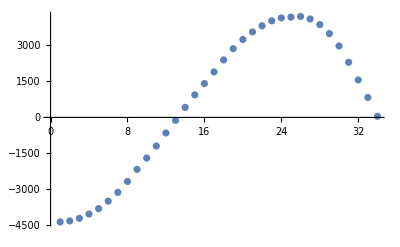

```mathematica
ListPlot[firIn]
```

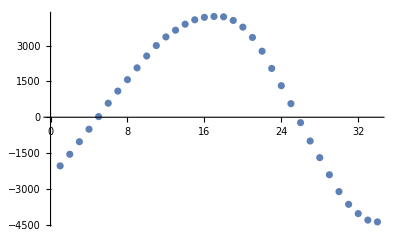

-Graphics-

```mathematica
firOut
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
LongestCommonSubsequence[firOutExp,firOut]
```

{}

```mathematica
s
```

s

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

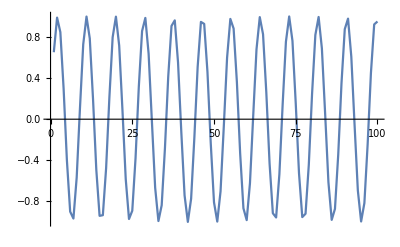

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Append[Flatten@Riffle[in,0],0]
```

{0.651834,0,0.988652,0,0.847678,0,0.297042,0,-0.397148,0,-0.899405,0,-0.967001,0,-0.567269,0,0.106611,0,0.728969,0,0.999033,0,0.786288,0,0.193549,0,-0.492727,0,-0.940881,0,-0.934329,0,-0.476238,0,0.212007,0,0.797794,0,0.998027,0,0.715936,0,0.0878512,0,-0.58269,0,-0.971632,0,-0.891007,0,-0.379779,0,0.314987,0,0.857527,0,0.985645,0,0.637424,0,-0.0188484,0,-0.666012,0,-0.991308,0,-0.837528,0,-0.278991,0,0.414376,0,0.907484,0,0.962028,0,0.551646,0,-0.125333,0,-0.741742,0,-0.999684,0,-0.774503,0,-0.175023,0,0.509041,0,0.947098,0,0.927445,0,0.45958,0,-0.230389,0,-0.809017,0,-0.996666,0,-0.70265,0,-0.06906,0,0.597905,0,0.975917,0,0.882291,0,0.362275,0,-0.33282,0,-0.867071,0,-0.982287,0,-0.622788,0,0.0376902,0,0.679953,0,0.993611,0,0.827081,0,0.260842,0,-0.431456,0,-0.915241,0,-0.956712,0,-0.535827,0,0.144011,0,0.754251,0,0.99998,0,0.762443,0,0.156434,0,-0.525175,0,-0.952979,0,-0.920232,0,-0.442758,0,0.24869,0,0.819952,0,0.994951,0,0.689114,0,0.0502443,0,-0.612907,0,-0.979855,0,-0.873262,0,-0.344643,0,0.350534,0,0.876307,0,0.978581,0,0.60793,0,-0.0565185,0,-0.693653,0,-0.995562,0,-0.816339,0,-0.242599,0,0.448383,0,0.922673,0,0.951057,0}

```mathematica
out=ListConvolve[fupker/2^16,inR,1,0];
```

```mathematica
LinInt[list_]:=Module[{i,intlist={}},For[i=1,i< Length[list],i++,AppendTo[intlist,list[[i]]];AppendTo[intlist,(list[[i]]+list[[i+1]])/2]];AppendTo[intlist,Last[list]];AppendTo[intlist,2*Last[intlist]-intlist[[-2]]];intlist]
```

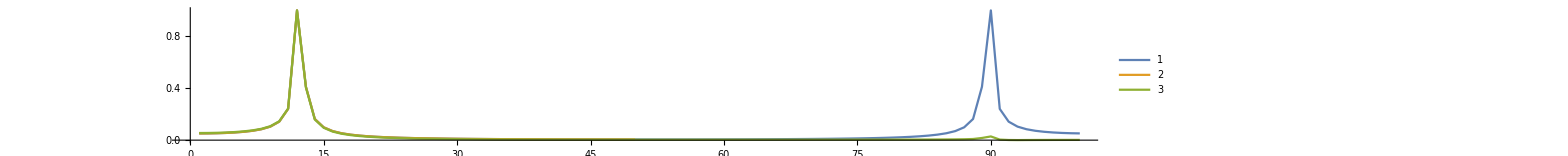

```mathematica
ListPlot[{Half@Abs@Fourier@inR/Max[Half@Abs@Fourier@inR],(Half@Abs@Fourier@in)/Max[Half@Abs@Fourier@in],(Half@Abs@Fourier@LinInt@in)/Max[Half@Abs@Fourier@LinInt@in]},Joined->True,PlotRange->All,ImageSize->5000, PlotLegends->Automatic,AspectRatio->0.1]
```

```mathematica
Manipulate[ListPlot[Abs@Fourier@Flatten@Riffle[Sin[2*π*f*#]&/@Range[100],{{0,0}}],Joined->True,ImageSize->300,PlotRange->{0,3}],{f,0,0.5,0.01}]
```

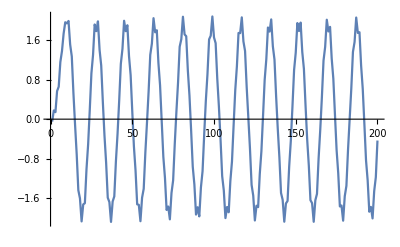

```mathematica
ListPlot[out,Joined->True]
```